# Higgs to two photon

### Initialization

```mathematica
Quit[];
```

```mathematica
$Language="English";
SetDirectory[NotebookDirectory[]];
<<FeynArts`
<<FormCalc`
```

FeynArts 3.10 (12 Mar 2018)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.6 (16 Apr 2018)

by Thomas Hahn

### h → γ γ Matrix Element Calculation

loading generic model file /Users/misho/.ghq/github.com/HEPcodes/FeynArts/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /Users/misho/.ghq/github.com/HEPcodes/FeynArts/Models/SM.mod

$CKM=False

> 46 particles (incl. antiparticles) in 16 classes

> $CounterTerms are ON

> 88 vertices

> 115 counterterms of order 1

> 6 counterterms of order 2

classes model {SM} initialized

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 22 Particles insertions

> Top. 2: 2 Particles insertions

> Top. 3: 2 Particles insertions

> Top. 4: 2 Particles insertions

Restoring 18 field point(s)

in total: 28 Particles insertions

> Top. 1 ad/becf/dedfef.m, 22 diagrams

> Top. 2 ad/bece/dede.m, 2 diagrams

> Top. 3 ad/becd/eded.m, 2 diagrams

> Top. 4 ad/bdce/eded.m, 2 diagrams

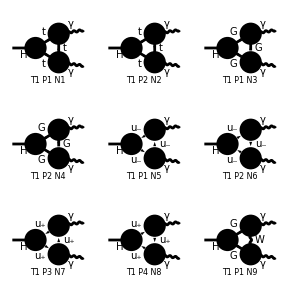

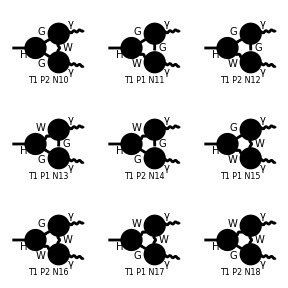

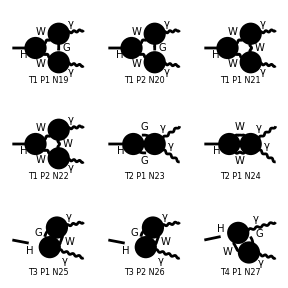

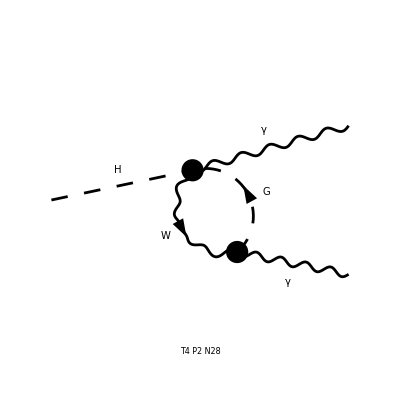

```mathematica
topo1=CreateTopologies[1,1->2,ExcludeTopologies->{Internal}];
diag1=InsertFields[topo1,{S[1]}->{V[1],V[1]},InsertionLevel->{Particles},Restrictions->NoLightFHCoupling];
Paint[diag1];
```

```mathematica
ClearProcess[];
amp=CalcFeynAmp[CreateFeynAmp[diag1],FermionChains->Chiral]
```

creating amplitudes at level(s) {Particles}

> Top. 1: 22 Particles amplitudes

> Top. 2: 2 Particles amplitudes

> Top. 3: 2 Particles amplitudes

> Top. 4: 2 Particles amplitudes

in total: 28 Particles amplitudes

preparing FORM code in /Users/misho/.ghq/github.com/misho104/FeynLecture/fc-amp-1.frm

running FORM...

ok

Amp[{{S[1],k[1],MH,{}}}→{{V[1],k[2],0,{}},{V[1],k[3],0,{}}}][1/(π SW)Alfa EL (-1/4 MW Sub2 C0i[cc0,0,0,MH2,MW2,MW2,MW2]+Pair1 ((MT2 (4/3 B0i[bb0,0,MT2,MT2]-16/3 C0i[cc00,0,0,MH2,MT2,MT2,MT2]))/MW+Sub1 (-1/4 B0i[bb0,MH2,MW2,MW2]+C0i[cc00,0,0,MH2,MW2,MW2,MW2])+1/4 MH2 MW C0i[cc1,0,0,MH2,MW2,MW2,MW2])+(MT2 (-2/3 Abb3 C0i[cc0,0,0,MH2,MT2,MT2,MT2]-4/3 Abb4 C0i[cc2,0,0,MH2,MT2,MT2,MT2]))/MW+1/2 Sub3 C0i[cc2,0,0,MH2,MW2,MW2,MW2]+Pair2 Pair3 (-(16 MT2 (C0i[cc12,0,0,MH2,MT2,MT2,MT2]+C0i[cc22,0,0,MH2,MT2,MT2,MT2]))/(3 MW)+Sub1 (C0i[cc12,0,0,MH2,MW2,MW2,MW2]+C0i[cc22,0,0,MH2,MW2,MW2,MW2])))]

To confirm that this diagram converges...

```mathematica
UVDivergentPart[amp]
divergence=%[[1]]
```

Amp[{{S[1],k[1],MH,{}}}→{{V[1],k[2],0,{}},{V[1],k[3],0,{}}}][0]

0

PolarizationSum directory to the amplitude invokes SquaredME, HelicityME, and ColourME (with _Hel=0 option).
[but you should not do so because you will lose traceability; instead I recommend you to do step by step as before.]

```mathematica
mat=PolarizationSum[amp,GaugeTerms->False]//.Subexpr[]//.Abbr[]//Simplify
```

HelicityME::nomat: Warning: No matrix elements to compute.

ColourME::nomat: Warning: No matrix elements to compute.

preparing FORM code in /Users/misho/.ghq/github.com/misho104/FeynLecture/fc-pol-1.frm

running FORM...

ok

1/(18 MW2 π SW2)Alfa Alfa2 (-(-16 MT2 B0i[bb0,0,MT2,MT2]+3 (MH2+6 MW2) B0i[bb0,MH2,MW2,MW2]-8 MH2 MT2 C0i[cc0,0,0,MH2,MT2,MT2,MT2]+21 MH2 MW2 C0i[cc0,0,0,MH2,MW2,MW2,MW2]+64 MT2 C0i[cc00,0,0,MH2,MT2,MT2,MT2]-12 MH2 C0i[cc00,0,0,MH2,MW2,MW2,MW2]-72 MW2 C0i[cc00,0,0,MH2,MW2,MW2,MW2]-3 MH2 MW2 C0i[cc1,0,0,MH2,MW2,MW2,MW2]-16 MH2 MT2 C0i[cc2,0,0,MH2,MT2,MT2,MT2]-6 MH2 MW2 C0i[cc2,0,0,MH2,MW2,MW2,MW2]) (16 MT2 B0i[bb0,0,MT2,MT2]^*-3 (MH2+6 MW2) B0i[bb0,MH2,MW2,MW2]^*+3 MH2 MW2 C0i[cc0,0,0,MH2,MW2,MW2,MW2]^*-64 MT2 C0i[cc00,0,0,MH2,MT2,MT2,MT2]^*+12 MH2 C0i[cc00,0,0,MH2,MW2,MW2,MW2]^*+72 MW2 C0i[cc00,0,0,MH2,MW2,MW2,MW2]^*+3 MH2 MW2 C0i[cc1,0,0,MH2,MW2,MW2,MW2]^*-32 MH2 MT2 C0i[cc12,0,0,MH2,MT2,MT2,MT2]^*+6 MH2^2 C0i[cc12,0,0,MH2,MW2,MW2,MW2]^*+36 MH2 MW2 C0i[cc12,0,0,MH2,MW2,MW2,MW2]^*-16 MH2 MT2 C0i[cc2,0,0,MH2,MT2,MT2,MT2]^*+6 MH2^2 C0i[cc2,0,0,MH2,MW2,MW2,MW2]^*+42 MH2 MW2 C0i[cc2,0,0,MH2,MW2,MW2,MW2]^*-32 MH2 MT2 C0i[cc22,0,0,MH2,MT2,MT2,MT2]^*+6 MH2^2 C0i[cc22,0,0,MH2,MW2,MW2,MW2]^*+36 MH2 MW2 C0i[cc22,0,0,MH2,MW2,MW2,MW2]^*)+2 MH2 (12 MW2 C0i[cc0,0,0,MH2,MW2,MW2,MW2]+18 MW2 C0i[cc2,0,0,MH2,MW2,MW2,MW2]-4 MT2 (C0i[cc0,0,0,MH2,MT2,MT2,MT2]+4 (C0i[cc12,0,0,MH2,MT2,MT2,MT2]+C0i[cc2,0,0,MH2,MT2,MT2,MT2]+C0i[cc22,0,0,MH2,MT2,MT2,MT2]))+18 MW2 (C0i[cc12,0,0,MH2,MW2,MW2,MW2]+C0i[cc22,0,0,MH2,MW2,MW2,MW2])+3 MH2 (C0i[cc12,0,0,MH2,MW2,MW2,MW2]+C0i[cc2,0,0,MH2,MW2,MW2,MW2]+C0i[cc22,0,0,MH2,MW2,MW2,MW2])) (16 MT2 B0i[bb0,0,MT2,MT2]^*-3 (MH2+6 MW2) B0i[bb0,MH2,MW2,MW2]^*-8 MH2 MT2 C0i[cc0,0,0,MH2,MT2,MT2,MT2]^*+27 MH2 MW2 C0i[cc0,0,0,MH2,MW2,MW2,MW2]^*-64 MT2 C0i[cc00,0,0,MH2,MT2,MT2,MT2]^*+12 MH2 C0i[cc00,0,0,MH2,MW2,MW2,MW2]^*+72 MW2 C0i[cc00,0,0,MH2,MW2,MW2,MW2]^*+3 MH2 MW2 C0i[cc1,0,0,MH2,MW2,MW2,MW2]^*-64 MH2 MT2 C0i[cc12,0,0,MH2,MT2,MT2,MT2]^*+12 MH2^2 C0i[cc12,0,0,MH2,MW2,MW2,MW2]^*+72 MH2 MW2 C0i[cc12,0,0,MH2,MW2,MW2,MW2]^*-48 MH2 MT2 C0i[cc2,0,0,MH2,MT2,MT2,MT2]^*+12 MH2^2 C0i[cc2,0,0,MH2,MW2,MW2,MW2]^*+78 MH2 MW2 C0i[cc2,0,0,MH2,MW2,MW2,MW2]^*-64 MH2 MT2 C0i[cc22,0,0,MH2,MT2,MT2,MT2]^*+12 MH2^2 C0i[cc22,0,0,MH2,MW2,MW2,MW2]^*+72 MH2 MW2 C0i[cc22,0,0,MH2,MW2,MW2,MW2]^*))

### Numerical Evaluation

```mathematica
Install["LoopTools"]
```

====================================================
   FF 2.0, a package to evaluate one-loop integrals
 written by G. J. van Oldenborgh, NIKHEF-H, Amsterdam
 ====================================================
 for the algorithms used see preprint NIKHEF-H 89/17,
 'New Algorithms for One-loop Integrals', by G.J. van
 Oldenborgh and J.A.M. Vermaseren, published in 
 Zeitschrift fuer Physik C46(1990)425.
 ====================================================

LinkObject[…]

```mathematica
VALUES[higgs_]:={
Den[p2_,m2_]:>1/(p2-m2),
MT->173,MT2->173^2,
MW->80.4,MW2->80.4^2,
Alfa->1/128,Alfa2->1/128^2,
SW2->0.23,
MH->higgs,MH2->higgs^2}
MyMatrixElement[higgs_]:=mat//.VALUES[higgs]//Simplify
```

```mathematica
MyMatrixElement[125]
```

0.131154

### Compare to a literature

```mathematica
f[t_]:=If[t<1,-1/4(Log[(1+√(1-t))/(1-√(1-t))]-ⅈ π)^2,(ArcSin[√(1/t)])^2]
Fb[t_]:=2+3t+3t(2-t)f[t]
Ff[t_]:=-2t(1+(1-t)f[t])
Fs[t_]:=t(1-t f[t])
InSomePaper[higgs_]:=(Alfa MH2^2)/(8π SW2 MW2)Abs[Alfa*3*(2/3)^2 Ff[((2MT)/MH)^2]+Alfa*1*1^2 Fb[((2MW)/MH)^2]]^2//.VALUES[higgs]
```

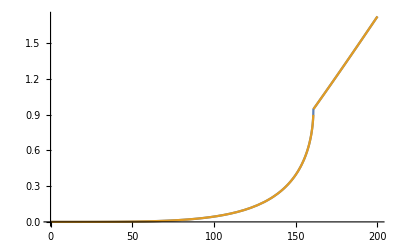

```mathematica
Plot[{MyMatrixElement[mh],InSomePaper[mh]},{mh,0,200}]
```

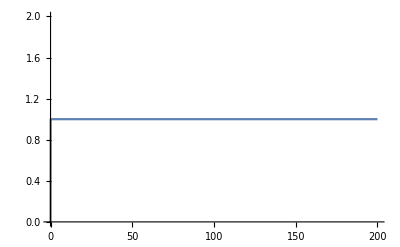

```mathematica
Plot[{MyMatrixElement[mh]/InSomePaper[mh]},{mh,0,200},PlotRange->{{0,200},{0,2}}]
```

The partial decay rate will be:

```mathematica
MyDecayRate[higgs_]:=1/(32π higgs)MyMatrixElement[higgs]
```

```mathematica
MyDecayRate[125]
```

0.0000104369

Compare this value with literature!

Of course we can (and should) ascertain the gauge independence. Here we utilize PaVeReduce.

```mathematica
ClearProcess[];
amp=CalcFeynAmp[CreateFeynAmp[diag1],FermionChains->Chiral,PaVeReduce->True]//.Subexpr[]//.Abbr[]
matWithGaugeTerms=PolarizationSum[amp,GaugeTerms->True]//.Subexpr[]//.Abbr[]//.Finite->1//FullSimplify
```

creating amplitudes at level(s) {Particles}

> Top. 1: 22 Particles amplitudes

> Top. 2: 2 Particles amplitudes

> Top. 3: 2 Particles amplitudes

> Top. 4: 2 Particles amplitudes

in total: 28 Particles amplitudes

preparing FORM code in /Users/misho/.ghq/github.com/misho104/FeynLecture/fc-amp-1.frm

running FORM...

ok

Amp[{{S[1],k[1],MH,{}}}→{{V[1],k[2],0,{}},{V[1],k[3],0,{}}}][-1/(π SW)Alfa EL (((MW+(2 MH2-2 (MH2-2 MW2)-5 MW2)/MW) (1/2 B0i[bb0,0,MW2,MW2]-1/2 B0i[bb0,MH2,MW2,MW2]) Pair[ec[2],k[1]] Pair[ec[3],k[1]])/MH2+1/12 Finite ((-24 MW+(16 MT2-3 (MH2-2 MW2))/MW) Pair[ec[2],ec[3]]+(2 (24 MW-(16 MT2-3 (MH2-2 MW2))/MW) Pair[ec[2],k[1]] Pair[ec[3],k[1]])/MH2)+1/4 C0i[cc0,0,0,MH2,MW2,MW2,MW2] ((-(2 (MH2-2 MW2) MW2)/MW+MW (MH2+2 MW2)) Pair[ec[2],ec[3]]+(4 (8 MW+(MH2-2 MW2)/MW) MW2 Pair[ec[2],k[1]] Pair[ec[3],k[1]])/MH2-MW (-7 MH2 Pair[ec[2],ec[3]]+18 MW2 Pair[ec[2],ec[3]]+16 Pair[ec[2],k[1]] Pair[ec[3],k[1]]))+(2 MT2 C0i[cc0,0,0,MH2,MT2,MT2,MT2] (-MH2 Pair[ec[2],ec[3]]+2 Pair[ec[2],k[1]] Pair[ec[3],k[1]]-4 MT2 (-Pair[ec[2],ec[3]]+(2 Pair[ec[2],k[1]] Pair[ec[3],k[1]])/MH2)))/(3 MW))]

HelicityME::nomat: Warning: No matrix elements to compute.

ColourME::nomat: Warning: No matrix elements to compute.

preparing FORM code in /Users/misho/.ghq/github.com/misho104/FeynLecture/fc-pol-1.frm

running FORM...

ok

1/(18 MW2 π SW2)Alfa Alfa2 (3 MH2-16 MT2+18 MW2+8 (MH2-4 MT2) MT2 C0i[cc0,0,0,MH2,MT2,MT2,MT2]-18 (MH2-2 MW2) MW2 C0i[cc0,0,0,MH2,MW2,MW2,MW2]) (3 MH2-16 MT2+18 MW2+8 (MH2-4 MT2) MT2 C0i[cc0,0,0,MH2,MT2,MT2,MT2]^*-18 (MH2-2 MW2) MW2 C0i[cc0,0,0,MH2,MW2,MW2,MW2]^*)